```mathematica
Needs["NumericalCalculus`"];
```

## Precompute joint element

```mathematica
precomputeElement[EJ1_,EJ2_]:=Module[{t1,ϕ,ϕ1,int1,res},
t1=Monitor[Table[
res=Table[
FindMinimum[-EJ1 Cos[ϕ1]-EJ2 Cos[ϕ-ϕ1], {ϕ1, s1}][[1]]
,{s1,-π,π,π/3.}];
{ϕ, Min[res]}
,{ϕ,-2π,2.π,π/1000.}],ϕ];
Return[Interpolation[t1]];
(*Return[t1];*)
];

getEnergy[int1_, ϕ_]:=Module[{},
Return[int1[Mod[ϕ+2π,4π]-2π]];
];
getEnergyJJ[EJ_, ϕ_]:=Module[{},
Return[-EJ*Cos[ϕ]];
];
getEnergyLinInd[EL_, ϕ_]:=Module[{},
Return[EL/2 ϕ^2];
];
```

## Set up

In the unit of GHz

```mathematica
sf=10^-9/(2 π 1*10^-34);
Ic1=Quantity[0.7*10^-6,"Ampere"];
EJ1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))Ic1 1/Quantity["Joule"],"SI"]
(*EJ2=α EJ1*)
(*EL=β EJ1*)
```

366.652

```mathematica
Quiet[
t1=Monitor[Table[precomputeElement[EJ1,α EJ1],{α,{0.5,2/3}}],α];
t2=Monitor[Table[precomputeElement[EJ1,α EJ1],{α,1,2,0.5}],α];
];
```

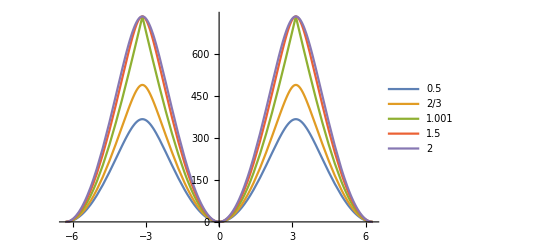

```mathematica
t=Flatten[{Table[getEnergy[t1[[i]],x]-getEnergy[t1[[i]],0],{i,1,Length[t1]}],Table[getEnergy[t2[[i]],x]-getEnergy[t2[[i]],0],{i,1,Length[t2]}]}];
Plot[Evaluate[t],{x,-2π,2π},PlotLegends->{"0.5","2/3","1.001","1.5","2"}]
```

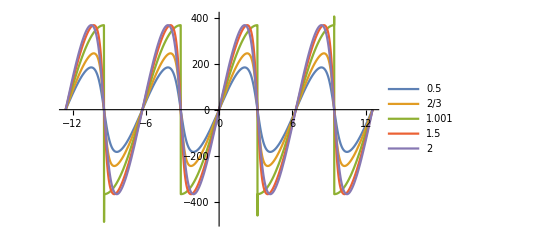

```mathematica
Plot[Evaluate[Table[D[t[[i]],x]/.x->y,{i,1,Length[t]}]],{y,-4π,4π},PlotLegends->{"0.5","2/3","1.001","1.5","2"}]
```

```mathematica
H=H[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕext_]:=
(getEnergyJJ[t[[1]],ϕ1-ϕ2-ϕext/4]+getEnergyJJ[t[[1]],ϕ2-ϕ3-ϕext/4]+ getEnergyJJ[t[[1]],ϕ3-ϕ4-ϕext/4]+getEnergyJJ[t[[1]],ϕ4-ϕ1-ϕext/4])+(getEnergyLinInd[EL,ϕ1-ϕ5]+getEnergyLinInd[EL,ϕ2-ϕ5]+getEnergyLinInd[EL,ϕ3-ϕ5]+getEnergyLinInd[EL,ϕ4-ϕ5]);
Hn[ϕ1_?NumericQ,ϕ2_?NumericQ,ϕ3_?NumericQ,ϕ4_?NumericQ,ϕ5_?NumericQ,ϕext_?NumericQ]:=(getEnergyJJ[t[[1]],ϕ1-ϕ2-ϕext/4]+getEnergyJJ[t[[1]],ϕ2-ϕ3-ϕext/4]+ getEnergyJJ[t[[1]],ϕ3-ϕ4-ϕext/4]+getEnergyJJ[t[[1]],ϕ4-ϕ1-ϕext/4])+(getEnergyLinInd[EL,ϕ1-ϕ5]+getEnergyLinInd[EL,ϕ2-ϕ5]+getEnergyLinInd[EL,ϕ3-ϕ5]+getEnergyLinInd[EL,ϕ4-ϕ5]);
Subscript[H, shunt]=EL/2(Subscript[φ, L1]^2+Subscript[φ, L2]^2+Subscript[φ, L3]^2+Subscript[φ, L4]^2);
Subscript[H, J]=-EJ(Cos[Subscript[φ, a1]]+Cos[Subscript[φ, a2]]+Cos[Subscript[φ, b1]]+Cos[Subscript[φ, b2]]+Cos[Subscript[φ, c1]]+Cos[Subscript[φ, c2]]+Cos[Subscript[φ, d1]]+Cos[Subscript[φ, d2]]);
```